```mathematica
Gx={{-1,0,1},{-2,0,2},{-1,0,1}};
Gy={{1,2,1},{0,0,0},{-1,-2,-1}};
particles=Import["D:\\Files\\research\\thesis\\runs\\c5_new\\inputs\\particles\\particles.mat"];
Dimensions/@particles
```

{{136,256,256},{136,256,256},{200,1},{200,1},{1,256},{1,256},{136,6}}

(13 π)/125

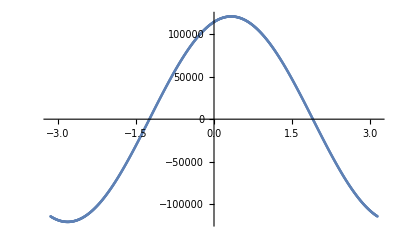

```mathematica
Qit=particles[[2,10]];
edginess=Table[{θ,Total[Cos[θ]Abs[ListConvolve[Gx,Qit]]+Sin[θ]Abs[ListConvolve[Gy,Qit]],2]},{θ,-π,π,2π/1000}];
θmax=edginess[[Flatten[Position[#,Max[#]]&@edginess[[;;,2]]],1]][[1]]
ListPlot[edginess]
```

```mathematica
edges=Cos[θmax]Abs[ListConvolve[Gx,Qit]]+Sin[θmax]Abs[ListConvolve[Gy,Qit]];
ListDensityPlot[Transpose@edges,PlotLegends->Automatic,InterpolationOrder->0]
```

-Graphics-

```mathematica
Manipulate[ListLinePlot[edges[[i]]],{i,1,254,1}]
```

Part::partd: Part specification edges⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: edges⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification edges⟦243⟧ is longer than depth of object.

ListLinePlot::lpn: edges⟦243⟧ is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[
peaks=Flatten[Position[PeakDetect[edges[[i]],σ,s],1]];
Show[
ListLinePlot[edges[[i]]]
,ListPlot[{#,edges[[i,#]]}&/@peaks,PlotStyle->Red]
]
,{i,1,254,1}
,{{σ,10},1,100}
,{{s,0.01},0.001,0.01}]
```

Part::partd: Part specification edges⟦203⟧ is longer than depth of object.

PeakDetect::arg: The argument edges⟦203⟧ at position 1 is not a consistent list of real values.

Part::partd: Part specification edges⟦203⟧ is longer than depth of object.

ListLinePlot::lpn: edges⟦203⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[edges⟦203⟧],].

```mathematica
boundaries=Table[Transpose[{{i,i},Flatten[Position[PeakDetect[edges[[i]],10,0.01],1]]}],{i,1,254}];
```

```mathematica
Show[
ListDensityPlot[Transpose@Qit,PlotLegends->Automatic,InterpolationOrder->0]
,ListLinePlot[{
boundaries[[;;,1]]
,boundaries[[;;,2]]
}]
]
```

-Graphics-

```mathematica
Manipulate[
Qit=particles[[2,t]];
edginess=Table[{θ,Total[Cos[θ °]Abs[ListConvolve[Gx,Qit]]+Sin[θ °]Abs[ListConvolve[Gy,Qit]],2]},{θ,-90,90,1}];
θmax=edginess[[Flatten[Position[#,Max[#]]&@edginess[[;;,2]]],1]][[1]];
edges=Cos[θmax °]Abs[ListConvolve[Gx,Qit]]+Sin[θmax °]Abs[ListConvolve[Gy,Qit]];
boundaries=Table[Transpose[{{i,i},Flatten[Position[PeakDetect[edges[[i]],10,0.01],1]]}],{i,1,254}];
,{t,1,136,1}]
```

## Old

```mathematica
QQ=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\aurora_longsharc_bent_01\\inputs\\particles\\20150201_36000.000000.h5","/Qp"];
```

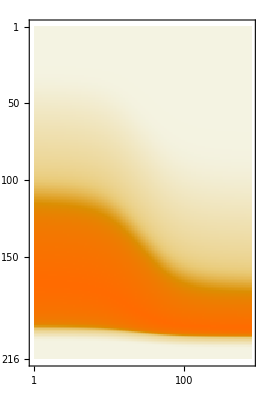

```mathematica
MatrixPlot[QQ]
```

```mathematica
r={40,369,214,262};
s={2,54,39,27};
```

```mathematica
77s/r//N
```

{3.85,11.2683,14.0327,7.93511}

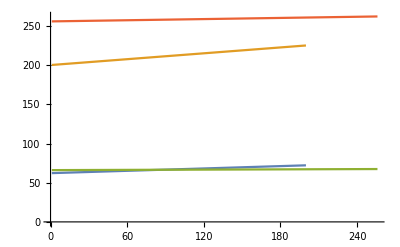

```mathematica
ListLinePlot[{
Flatten[particles[[3]]]
,Flatten[particles[[4]]]+360
,Flatten[particles[[5]]]
,Flatten[particles[[6]]]
}
]
```

```mathematica
Manipulate[
mat=particles[[2,1]];
edges=Cos[θ]ListConvolve[Gx,mat]+Sin[θ]ListConvolve[Gy,mat];
MatrixPlot[edges]
,{θ,-π/2,π/2}]
```

```mathematica
Manipulate[
mat=particles[[2,t]];
edges=Cos[θ]Abs[ListConvolve[Gx,mat]]+Sin[θ]Abs[ListConvolve[Gy,mat]];
maxedgesX=Transpose[{Flatten[Position[#,Max[#]]&/@edges],Reverse@Range[Length[edges]]}];
maxedgesY=Transpose[{Range[Length[edges]],Flatten[Position[#,Max[#]]&/@Transpose@Reverse@edges]}];
points=Cases[Position[edges,e_/;e>1000],p_/;p[[1]]>2]/.{x_,y_}->{y,254-x};
Show[
MatrixPlot[edges,PlotLabel->ToString[Total[edges,2]/10^8],PlotLegends->Automatic]
,Graphics[{Red,Point[maxedgesX]}]
,Graphics[{Blue,Point[maxedgesY]}]
(*,Graphics[{Green,Point[points]}]*)
]
,{t,1,Length[particles[[1]]],1}
,{{θ,7π/50},0,π/2}
]
```

```mathematica
Manipulate[ListLinePlot[{edges[[x]],edges[[;;,y]]}],{x,1,Length[edges],1},{y,1,Length[edges],1}]
```

```mathematica
Manipulate[
points=Table[{i,Round[0.2i]+t},{i,1,Length[edges]}];
Show[
MatrixPlot[edges,PlotLabel->{points[[1]],points[[-1]]}]
,Graphics[Point[points]]
]
,{t,1,Length[edges]-Round[0.2Length[edges]]}]
```

```mathematica
edges[[#1,#2]]&@@@points//Dimensions
```

{254}

```mathematica
Manipulate[
points=Table[{i,Round[0.2i]+t},{i,1,Length[edges]}];
ListLinePlot[edges[[#1,#2]]&@@@points]
,{t,1,Length[edges]-Round[0.2Length[edges]]}]
```

Part::pkspec1: The expression 36.3 cannot be used as a part specification.

Part::pkspec1: The expression 37.3 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression 36.3 cannot be used as a part specification.

Part::pkspec1: The expression 37.3 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression 36.3 cannot be used as a part specification.

Part::pkspec1: The expression 37.3 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

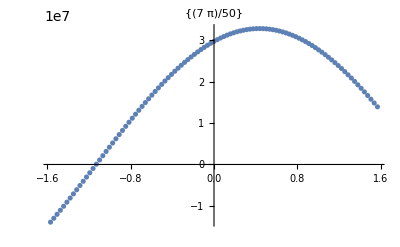

```mathematica
edgesmax=Table[{θ,Total[Cos[θ]Abs[ListConvolve[Gx,mat]]+Sin[θ]Abs[ListConvolve[Gy,mat]],2]},{θ,-π/2,π/2,π/100}];
ListPlot[edgesmax,PlotLabel->edgesmax[[Flatten[Position[edgesmax[[;;,2]],Max[edgesmax]]],1]]]
```

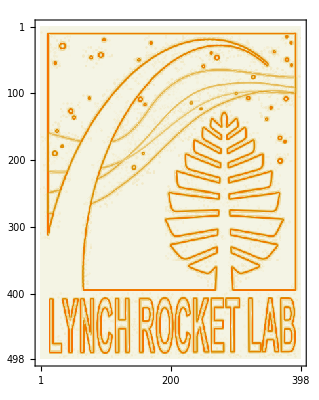

```mathematica
test=Map[Norm,ImageData[Import["D:\\Files\\research\\logos\\lynch.png"]],{2}];
X=ListConvolve[Gx,test];
Y=ListConvolve[Gy,test];
M=Sqrt[X^2+Y^2];
MatrixPlot[M]
```